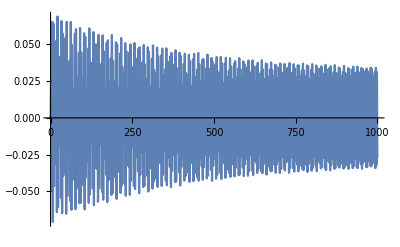

```mathematica
res=NDSolve[{y''[t]==-0.005y'[t]-2.4Cos[y[t]]Sin[y[t]]+0.05Sin[2t],y[0]==0.0001,y'[0]==0},y,{t,0,1000}];
Plot[y[t]/.res,{t,0,1000},ImageSize->Full]
```

```mathematica
pics=Table[Graphics[Rotate[Rectangle[{-2,0},{2,0.3}],First[(θ[t]/.res)]],PlotRange->{{-5,5},{-5,5}},ImageSize->Large],{t,10,35,0.033}];
ListAnimate[pics]
```

```mathematica
Export["test.mov",pics]
```

test.mov

```mathematica
Anim
```

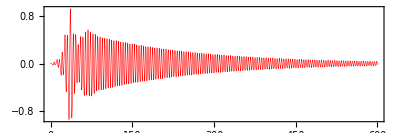

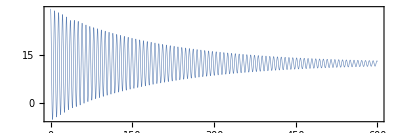

```mathematica
ClearAll["Global‘*"];
d=0.01;m=2500;l=6;K=1000; μ=2.6;λ=0.02;g=9.8;
res=NDSolve[{θ''[t]==-d θ'[t]+3 K/(m l)Cos[θ[t]](Max[y[t]-l Sin[θ[t]],0]    -  Max[y[t]+l Sin[θ[t]],0] )+λ Sin[μ t],
y''[t]==- d y'[t]-(K/m) (Max[y[t]-l Sin[θ[t]],0]    +  Max[y[t]+l Sin[θ[t]],0] )+g +λ Sin[μ t],y[0]==29,y'[0]==0,θ[0]==0.001,θ'[0]==0},{θ[t],y[t]},{t,0,1000}];
Plot[θ[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Red,Thickness[0.001]],Frame->True,FrameStyle->Directive[20]]
Plot[y[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Thickness[0.001]],Frame->True,FrameStyle->Directive[20]]
```